# Duffing equation solver

P. Huft

Implements the method described in Qaisi paper to solve the Duffing eq by power expansion.
m dx^2/dt + alpha x + beta x^3 = F cos(wf t). m=1 in the Qaisi example.

## Check with Qaisi paper params

```mathematica
(*PARAMS*)
α=4;
β=1;
F=0.212;
ωf=3;
v0=0;
x0=0;
terms =10; (*number of terms to represent x*)
```

```mathematica
(*COMPUTE POWER SERIES SOLUTION*)
Clear[ω];
alist={x0,v0/ω};(*coeffs for power series of x*)
b1 =Coefficient[Collect[Sum[alist[[i]] τ^(i-1),{i,1,Length[alist]}]^3,τ],τ,0];
b2 = Coefficient[Collect[Sum[alist[[i]] τ^(i-1),{i,1,Length[alist]}]^3,τ],τ,1];
blist ={b1,b2};(*coeffs for power series exp of x^3*)
clist={1,0};(*coeffs for power series exp of force term*)
(*ω below is computed later, after we've found the symbolic coefficients ak,bk, and ck*)
ck2[k_]:=(((k-1)^2-(ωf/ω)^2)/(k(k+1)))clist[[k]];(*k=1,2,..*)
ak2[k_]:=(((ω^2(k-1)^2-α)alist[[k]]-β blist[[k]] + F clist[[k]])/(k(k+1)ω^2));
x[coeffs_]:=Collect[Sum[coeffs[[i]] τ^(i-1),{i,1,Length[coeffs]}],τ];
(*the main loop to compute a,b,c's*)
For[k=1,k<terms+1,k++,
(*compute ak+2*)
AppendTo[alist,ak2[k]//FullSimplify];
(*compute bk+2 from updated alist*)
AppendTo[blist,Coefficient[x[alist]^3,τ,k-1]//FullSimplify];
(*compute ck+2*)
AppendTo[clist,ck2[k]//FullSimplify]
]
xτ=x[alist];
fτ  =F Collect[Sum[coeffs[[i]] τ^(i-1),{i,1,Length[coeffs]}],τ]/.coeffs->clist;
KE = 0.5 ω^2(1-τ^2)D[xτ,τ]^2;
PE = 0.5α xτ^2+0.25 β xτ^4;
W = fτ xτ;
L[ω_,τ_]:=KE-PE-W
(*Hamilton's principle-- this integral must be zero*)
```

```mathematica
alist
```

{0,0,0.106/ω^2,0.,(-0.114833+0.0353333 ω^2)/ω^4,0.,(0.0391611-0.0765556 ω^2+0.0188444 ω^4)/ω^6,0.,(-0.00663026+0.0391611 ω^2-0.0535889 ω^4+0.0121143 ω^6)/ω^8,0.,(0.000677982-0.00885358 ω^2+0.0339396 ω^4-0.0398575 ω^6+0.0086146 ω^8)/ω^10,0.}

```mathematica
action = Integrate[L[ω,τ]/ω 1/(√(1-τ^2)),{τ,0,1}]
```

1/ω^41(-1.04023×10^-14+9.60707×10^-13 ω^2-4.03606×10^-11 ω^4+1.02165×10^-9 ω^6-1.73995×10^-8 ω^8+2.10859×10^-7 ω^10-1.87551×10^-6 ω^12+0.00001245 ω^14-0.0000621154 ω^16+0.000232789 ω^18-0.000650682 ω^20+0.00134719 ω^22-0.00220865 ω^24+0.00459947 ω^26-0.0175257 ω^28+0.060428 ω^30-0.128003 ω^32+0.146081 ω^34-0.076811 ω^36+0.0133214 ω^38)

```mathematica
NSolve[D[action,ω]==0 && ω>0,ω,Reals]
```

{{ω→0.297813},{ω→0.316717},{ω→0.370757},{ω→0.410285},{ω→0.496662},{ω→0.604091},{ω→0.844798},{ω→1.2853},{ω→2.47764}}

```mathematica
alist
```

{0,0,0.106/ω^2,0.,(-0.114833+0.0353333 ω^2)/ω^4,0.,(0.0391611-0.0765556 ω^2+0.0188444 ω^4)/ω^6,0.,(-0.00663026+0.0391611 ω^2-0.0535889 ω^4+0.0121143 ω^6)/ω^8,0.,(0.000677982-0.00885358 ω^2+0.0339396 ω^4-0.0398575 ω^6+0.0086146 ω^8)/ω^10,0.}

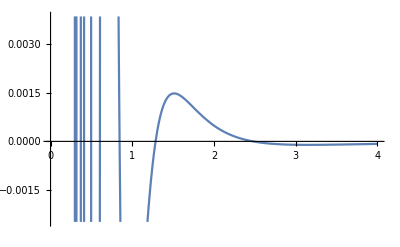

```mathematica
Plot[Evaluate[D[action,ω]],{ω,0,4}]
```

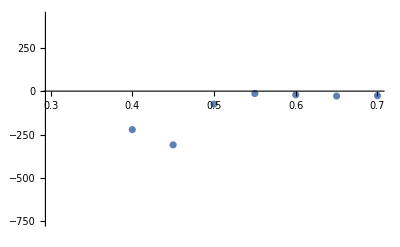

```mathematica
dt=0.2;
ListPlot[Transpose@@{{Range[0.3,0.7,0.05],Table[(Integrate[(KE-PE-W)/ω Series[1/(√(1-τ^2)),{τ,0,50}],{τ,0+dt,1+dt}]-Integrate[(KE-PE-W)/ω Series[1/(√(1-τ^2)),{τ,0,50}],{τ,0-dt,1-dt}])/dt,{ω,Range[0.3,0.7,0.05]}]}}]
```

```mathematica
alist/.ω->0.49666
```

{0,0,0.429722,0.,-1.74402,0.,1.42738,0.,-0.0132948,0.,-0.0078392,0.}

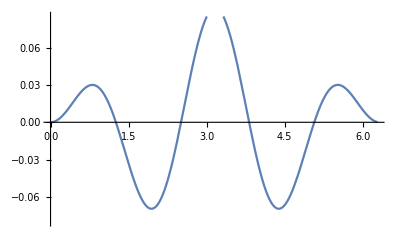

```mathematica
xt = Collect[Sum[alist[[i]] Sin[ω t]^(i-1),{i,1,Length[alist]}],Sin[ω t]]/.ω->0.49666;
Plot[xt,{t,0,3*2π/ωf},PlotRange->{-0.08,0.085}]
```

```mathematica
Clear[p,q];
KE = 0.5 ω^2(1-τ^2)p^2;
PE = 0.5α q^2+0.25 β q^4;
W = fτ q;
L = KE-PE - W;
```

```mathematica
Assuming[τ ϵ Reals,NSolve[Evaluate[(D[D[L,p]/.p->D[xτ,τ],τ]==D[L,q]/.q->xτ)],ω,Reals]]
```

$Aborted

```mathematica
(0.7071067811865476 √q √(4.+q^2))/(√p √τ)/.{q->xτ,p->D[xτ,τ]}//FullSimplify
```

(0.707107 √(1/ω^10 τ^2 (0.106 ω^8+τ^2 ω^6 (-0.114833+0.0353333 ω^2)+τ^4 ω^4 (0.0391611-0.0765556 ω^2+0.0188444 ω^4)+τ^6 ω^2 (-0.00663026+0.0391611 ω^2-0.0535889 ω^4+0.0121143 ω^6)+τ^8 (0.000677982-0.00885358 ω^2+0.0339396 ω^4-0.0398575 ω^6+0.0086146 ω^8))) √(4.+1/ω^20 0.0000742114 τ^4 (12.3047 ω^8+τ^2 ω^6 (-13.3301+4.10156 ω^2)+τ^4 ω^4 (4.5459-8.88672 ω^2+2.1875 ω^4)+τ^6 ω^2 (-0.769653+4.5459 ω^2-6.2207 ω^4+1.40625 ω^6)+τ^8 (0.0787014-1.02774 ω^2+3.93978 ω^4-4.62674 ω^6+1. ω^8))^2))/(√τ √(1/ω^10(0.212 τ ω^8+τ^3 ω^6 (-0.459333+0.141333 ω^2)+τ^5 ω^4 (0.234967-0.459333 ω^2+0.113067 ω^4)+τ^7 ω^2 (-0.0530421+0.313289 ω^2-0.428711 ω^4+0.0969143 ω^6)+τ^9 (0.00677982-0.0885358 ω^2+0.339396 ω^4-0.398575 ω^6+0.086146 ω^8))))

#### Solve ODE numerically

```mathematica
Clear[x]
```

```mathematica
s=NDSolve[{x''[t]+α x[t]+β x[t]^3==F Cos[ωf t],x[0]==0,x'[0]==0},x,{t,0,3*2π/ωf}]
```

{{x→InterpolatingFunction[…]}}

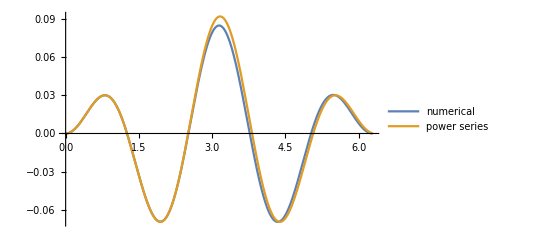

```mathematica
Plot[{Evaluate[x[t]/.s],xt},{t,0,3*2π/ωf},PlotRange->All,PlotLegends->{"numerical","power series"}]
```

## Quartic, non-driven oscillator

The axial equation of motion for an atom in a dark trap described by U = kB T | 1 - E_gaussian(rho,z) |^2  is given by dz^2/dt + (kB T/(m zR^4))z^4 = 0.

```mathematica
(*PARAMS*)
kB = 1.38*^-23;
T = 5*^-4;(*trap depth [K]*)
zR = π*(1*^-6)^2/8.08*^-7;(*[m]*)
mCs= 2.2069393×10^-25; (*[kg]*)
α=0;
β=kB T/(mCs zR^4);
F=.0;
ωf=.0;
v0=√(2 kB*40*^-6/mCs);(*initial speed guess = mean speed for 40 uK atom*)
x0=.0;
terms =13; (*number of terms to represent x*)
```

```mathematica
(*COMPUTE POWER SERIES SOLUTION*)
Clear[ω];
alist={x0,v0/ω};(*coeffs for power series of x*)
b1 =Coefficient[Collect[Sum[alist[[i]] τ^(i-1),{i,1,Length[alist]}]^3,τ],τ,0];
b2 = Coefficient[Collect[Sum[alist[[i]] τ^(i-1),{i,1,Length[alist]}]^3,τ],τ,1];
blist ={b1,b2};(*coeffs for power series exp of x^3*)
clist={1,0};(*coeffs for power series exp of force term*)
(*ω below is computed later, after we've found the symbolic coefficients ak,bk, and ck*)
ck2[k_]:=(((k-1)^2-(ωf/ω)^2)/(k(k+1)))clist[[k]];(*k=1,2,..*)
ak2[k_]:=(((ω^2(k-1)^2-α)alist[[k]]-β blist[[k]] + F clist[[k]])/(k(k+1)ω^2));
x[coeffs_]:=Collect[Sum[coeffs[[i]] τ^(i-1),{i,1,Length[coeffs]}],τ];
(*the main loop to compute a,b,c's*)
For[k=1,k<terms+1,k++,
(*compute ak+2*)
AppendTo[alist,ak2[k]//FullSimplify];
(*compute bk+2 from updated alist*)
AppendTo[blist,Coefficient[x[alist]^3,τ,k-1]//FullSimplify];
(*compute ck+2*)
AppendTo[clist,ck2[k]//FullSimplify]
]
xτ=x[alist];
fτ  =F Collect[Sum[coeffs[[i]] τ^(i-1),{i,1,Length[coeffs]}],τ]/.coeffs->clist;
KE = 0.5 ω^2(1-τ^2)D[xτ,τ]^2;
PE = 0.5α xτ^2+0.25 β xτ^4;
W = fτ xτ;
L[ω_,τ_]:=KE-PE-W;(*Hamilton's principle-- this integral must be zero*)
alist
```

Power::indet: Indeterminate expression 0.^0 encountered.

{0.,0.0707277/ω,0.,0.+0.0117879/ω,0.,0.+0.00530458/ω,0.,0.-(1.15245×10^15)/ω^5+0.00315749/ω,0.,0.-(1.12044×10^15)/ω^5+0.00214884/ω,0.,0.-(9.60727×10^14)/ω^5+0.00158233/ω,0.,0.+(1.51671×10^31)/ω^9-(8.11441×10^14)/ω^5+0.00122732/ω,0.}

```mathematica
action = Integrate[L[ω,τ]/ω 1/(√(1-τ^2)),{τ,0,1}]
```

1/ω^37(-3.13061×10^143+3.45218×10^128 ω^4-1.5201×10^113 ω^8+3.3875×10^97 ω^12-4.01429×10^81 ω^16+2.50521×10^65 ω^20-8.58322×10^48 ω^24+1.6632×10^32 ω^28-1.53596×10^15 ω^32+0.00317295 ω^36)

```mathematica
NSolve[D[action,ω]==0 && ω>0,ω,Reals]
```

{{ω→7914.78},{ω→9010.04},{ω→12225.6},{ω→17665.7},{ω→38575.7}}

```mathematica
Clear[x]
ω0=10000;
xt = Collect[Sum[alist[[i]] Sin[ω t]^(i-1),{i,1,Length[alist]}],Sin[ω t]]/.ω->ω0;
s=NDSolve[{x''[t]+α x[t]+β x[t]^3==F Cos[ωf t],x[0]==x0,x'[0]==v0},x,{t,0,3*2π/ω0}];
Plot[{Evaluate[x[t]/.s],xt},{t,0,3*2π/ω0},PlotRange->Automatic,PlotLegends->{"numerical","power series"}]
```

```mathematica
Clear[x]
ω0=29000;
guess= 3*10^-6*Sin[ω0 t];
s=NDSolve[{x''[t]+α x[t]+β x[t]^3==F Cos[ωf t],x[0]==1*^-6,x'[0]==v0},x,{t,0,3*2π/ω0}];
Plot[{Evaluate[x[t]/.s],guess},{t,0,3*2π/ω0},PlotRange->Automatic,PlotLegends->{"numerical","guess"}]
```

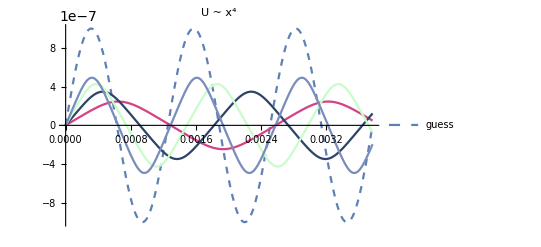

```mathematica
Clear[x]
ω0=5000;
guess= 1*10^-6*Sin[ω0 t];
guessplt=Plot[guess,{t,0,3*2π/ω0},PlotRange->Automatic,PlotStyle->Dashed,PlotLegends->{"guess"}];
plts = {};
For[i=1,i<5,i++,
speed0=0.01*i*√((kB *40*^-6)/mCs);
s=NDSolve[{x''[t]+α x[t]+β x[t]^3==F Cos[ωf t],x[0]==x0,x'[0]==speed0},x,{t,0,3*2π/ω0}];
AppendTo[plts,Plot[Evaluate[x[t]/.s],{t,0,3*2π/ω0},PlotStyle->RGBColor[RandomReal[],RandomReal[],RandomReal[]]]];
];
Show[guessplt,plts,PlotRange->All,PlotLabel->"U ~ x^4"]
```

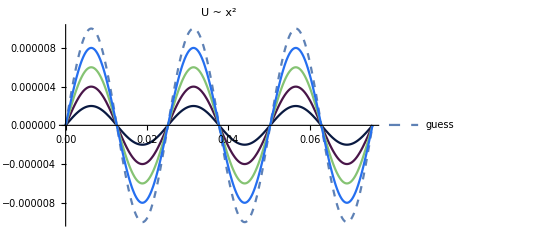

```mathematica
Clear[x]
ω0=250;
guess= 10*10^-6*Sin[ω0 t];
guessplt=Plot[guess,{t,0,3*2π/ω0},PlotRange->Automatic,PlotStyle->Dashed,PlotLegends->{"guess"}];
plts = {};
For[i=1,i<5,i++,
speed0=0.01*i*√((kB *40*^-6)/mCs);
s=NDSolve[{x''[t]+(kB 0.001)/(mCs 1*^-6) x[t]==0,x[0]==0,x'[0]==speed0},x,{t,0,3*2π/ω0}];
AppendTo[plts,Plot[Evaluate[x[t]/.s],{t,0,3*2π/ω0},PlotStyle->RGBColor[RandomReal[],RandomReal[],RandomReal[]]]];
];
Show[guessplt,plts,PlotRange->All,PlotLabel->"U ~ x^2"]
```

```mathematica
(*Plot[Abs[FourierTransform[x[t]/.s,t,ω]]^2,{ω,2π*1000,2π*30000}]*)
```

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in t in the region {{0.,-∞}}. NIntegrate obtained 1.05591×10^78+1.02718×10^78 ⅈ and 4.01234×10^78 for the integral and error estimates.

```mathematica
(2*^-6)^-1 √(kB T/mCs)
```

88409.6

```mathematica
xt
```

0.+(0.0707277 Sin[12127.2 t])/ω+(0.+0.0117879/ω) Sin[12127.2 t]^3+(0.+0.00530458/ω) Sin[12127.2 t]^5+(0.-(1.15245×10^15)/ω^5+0.00315749/ω) Sin[12127.2 t]^7+(0.-(1.12044×10^15)/ω^5+0.00214884/ω) Sin[12127.2 t]^9+(0.-(9.60727×10^14)/ω^5+0.00158233/ω) Sin[12127.2 t]^11